```mathematica
<<QI`
```

```mathematica
(*Package is used for partial tracing, can be obtained https://github.com/rogercolbeck/QI*)
```

```mathematica
KetZero = {1,0}
```

{1,0}

```mathematica
KetOne = {0,1}
```

{0,1}

```mathematica
KetPlus = (1/Sqrt[2])*(KetZero + KetOne)
```

{1/(√2),1/(√2)}

```mathematica
PZero = {{1,0},{0,0}}
```

{{1,0},{0,0}}

```mathematica
PPlus = 1/2*{{1,1},{1,1}}
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
(*A letter in an I.I.D sample from a source distribution where with probability 1/2 |0> or |+> are obtained*)
```

```mathematica
Letter =1/2*PZero + 1/2*PPlus
```

{{3/4,1/4},{1/4,1/4}}

```mathematica
{{3/4,1/4},{1/4,1/4}}//Eigensystem
```

{{1/4 (2+√2),1/4 (2-√2)},{{1+√2,1},{1-√2,1}}}

```mathematica
FullSimplify[Normalize[{1+√2,1}]]
```

{(√(2+√2))/2,1/(√(2 (2+√2)))}

```mathematica
{(√(2+√2))/2,1/(√(2 (2+√2)))}//N
```

{0.92388,0.382683}

```mathematica
(*Source von Neumann Entropy*)
```

```mathematica
FullSimplify[-(1/4 (2+√2))*Log2[1/4 (2+√2)]-(1/4 (2-√2))*Log2[1/4 (2-√2)]]
```

(-2 √2 ArcCoth[√2]+Log[64])/Log[16]

```mathematica
(-2 √2 ArcCoth[√2]+Log[64])/Log[16]//N
```

0.600876

```mathematica
2^(3*(0.6008760366928559))
```

3.48855

```mathematica
(*Only need 2 qubits to encode a 3 qubit message*)
```

```mathematica
(P0 ={{Cos[π/8]^2,Cos[π/8]*Sin[π/8]},{Cos[π/8]*Sin[π/8],Sin[π/8]^2}})//MatrixForm
```

(Cos[π/8]^2 | Cos[π/8] Sin[π/8]
Cos[π/8] Sin[π/8] | Sin[π/8]^2)

```mathematica
(P1 ={{Sin[π/8]^2,-Cos[π/8]*Sin[π/8]},{-Cos[π/8]*Sin[π/8],Cos[π/8]^2}})//MatrixForm
```

(Sin[π/8]^2 | -Cos[π/8] Sin[π/8]
-Cos[π/8] Sin[π/8] | Cos[π/8]^2)

```mathematica
(Ket0 ={Cos[π/8],Sin[π/8]})//MatrixForm
```

(Cos[π/8]
Sin[π/8])

```mathematica
(Ket1 ={Sin[π/8],-Cos[π/8]})//MatrixForm
```

(Sin[π/8]
-Cos[π/8])

```mathematica
(*Hamming weight up to 1 one projectors*)
```

```mathematica
(P000 = FullSimplify[KroneckerProduct[P0,P0,P0]])//MatrixForm;
(P010 = FullSimplify[KroneckerProduct[P0,P1,P0]])//MatrixForm;
(P001 = FullSimplify[KroneckerProduct[P0,P0,P1]])//MatrixForm;
(P100 = FullSimplify[KroneckerProduct[P1,P0,P0]])//MatrixForm;
```

```mathematica
(*Typical projector is the sum of these projectors*)
```

```mathematica
TypicalProjector = FullSimplify[(P000)+(P001+P010+P100)];
```

```mathematica
aTypicalProjector = FullSimplify[IdentityMatrix[8]-(P000+P001+P010+P100)];
```

```mathematica
(*Measurement Unitary*)
```

```mathematica
CompUni = FullSimplify[ArrayFlatten[{{TypicalProjector,IdentityMatrix[8]-TypicalProjector},{IdentityMatrix[8]-TypicalProjector,TypicalProjector}}]];
```

```mathematica
(*Messages*)
```

```mathematica
(Message1 =KroneckerProduct[PZero,PZero,PZero])//MatrixForm;
(Message2 =KroneckerProduct[PPlus,PZero,PZero])//MatrixForm;
(Message3 =KroneckerProduct[PZero,PPlus,PZero])//MatrixForm;
(Message4 =KroneckerProduct[PZero,PZero,PPlus])//MatrixForm;
(Message5 =KroneckerProduct[PPlus,PPlus,PZero])//MatrixForm;
(Message6 =KroneckerProduct[PZero,PPlus,PPlus])//MatrixForm;
(Message7=KroneckerProduct[PPlus,PZero,PPlus])//MatrixForm;
(Message8 =KroneckerProduct[PPlus,PPlus,PPlus])//MatrixForm;
```

```mathematica
(*Pre-Measurement State : Probe Ancilla + Message*)
```

```mathematica
PreMeasurementState = KroneckerProduct[PZero,Message5];
```

```mathematica
PostMeasurementState =FullSimplify[CompUni.PreMeasurementState.ConjugateTranspose[CompUni]];
```

```mathematica
H[ω_] =-ω*PauliMatrix[3] ;
```

```mathematica
ThermalState[β_,ω_] =MatrixExp[-β*H[ω]] /Tr[MatrixExp[-β*H[ω]]];
```

```mathematica
PreMeasurementStateThermal[β_,ω_] = KroneckerProduct[ThermalState[β,ω],Message5];
```

```mathematica
PostMeasurementStateThermal[β_,ω_] =FullSimplify[CompUni.PreMeasurementStateThermal[β,ω].ConjugateTranspose[CompUni]];
```

```mathematica
ProbePostMeasurementStateProbeThermal[β_,ω_] =FullSimplify[PartialTrace[PostMeasurementStateThermal[β,ω] ,2,8,2]] ;
```

```mathematica
PostMeasurementStateMessage=FullSimplify[PartialTrace[KroneckerProduct[PZero,IdentityMatrix[8] ].PostMeasurementState,2,8,1]];
```

```mathematica
(*Let's construct the encoding unitary*)
C1 = Flatten[KroneckerProduct[Ket0,Ket0,Ket0]]; (*to be sent to 000*)
C2 =Flatten[KroneckerProduct[Ket1,Ket0,Ket0]]; (*to be sent to 100*)
C3 = Flatten[KroneckerProduct[Ket0,Ket1,Ket0]]; (*to be sent to 010*)
C4 =Flatten[KroneckerProduct[Ket1,Ket1,Ket0]]; (*to be sent to 001*)
C5 =Flatten[KroneckerProduct[Ket0,Ket0,Ket1]]; (*to be sent to 110*)
C6 =Flatten[KroneckerProduct[Ket1,Ket0,Ket1]]; (*to be sent to 011*)
C7=Flatten[KroneckerProduct[Ket0,Ket1,Ket1]]; (*to be sent to 101*)
C8=Flatten[KroneckerProduct[Ket1,Ket1,Ket1]];(*to be sent to 111*)
```

```mathematica
(Encoder = Transpose[{C1,C2,C3,C4,C5,C6,C7,C8}])//MatrixForm
```

(Cos[π/8]^3 | Cos[π/8]^2 Sin[π/8] | Cos[π/8]^2 Sin[π/8] | Cos[π/8] Sin[π/8]^2 | Cos[π/8]^2 Sin[π/8] | Cos[π/8] Sin[π/8]^2 | Cos[π/8] Sin[π/8]^2 | Sin[π/8]^3
Cos[π/8]^2 Sin[π/8] | Cos[π/8] Sin[π/8]^2 | Cos[π/8] Sin[π/8]^2 | Sin[π/8]^3 | -Cos[π/8]^3 | -Cos[π/8]^2 Sin[π/8] | -Cos[π/8]^2 Sin[π/8] | -Cos[π/8] Sin[π/8]^2
Cos[π/8]^2 Sin[π/8] | Cos[π/8] Sin[π/8]^2 | -Cos[π/8]^3 | -Cos[π/8]^2 Sin[π/8] | Cos[π/8] Sin[π/8]^2 | Sin[π/8]^3 | -Cos[π/8]^2 Sin[π/8] | -Cos[π/8] Sin[π/8]^2
Cos[π/8] Sin[π/8]^2 | Sin[π/8]^3 | -Cos[π/8]^2 Sin[π/8] | -Cos[π/8] Sin[π/8]^2 | -Cos[π/8]^2 Sin[π/8] | -Cos[π/8] Sin[π/8]^2 | Cos[π/8]^3 | Cos[π/8]^2 Sin[π/8]
Cos[π/8]^2 Sin[π/8] | -Cos[π/8]^3 | Cos[π/8] Sin[π/8]^2 | -Cos[π/8]^2 Sin[π/8] | Cos[π/8] Sin[π/8]^2 | -Cos[π/8]^2 Sin[π/8] | Sin[π/8]^3 | -Cos[π/8] Sin[π/8]^2
Cos[π/8] Sin[π/8]^2 | -Cos[π/8]^2 Sin[π/8] | Sin[π/8]^3 | -Cos[π/8] Sin[π/8]^2 | -Cos[π/8]^2 Sin[π/8] | Cos[π/8]^3 | -Cos[π/8] Sin[π/8]^2 | Cos[π/8]^2 Sin[π/8]
Cos[π/8] Sin[π/8]^2 | -Cos[π/8]^2 Sin[π/8] | -Cos[π/8]^2 Sin[π/8] | Cos[π/8]^3 | Sin[π/8]^3 | -Cos[π/8] Sin[π/8]^2 | -Cos[π/8] Sin[π/8]^2 | Cos[π/8]^2 Sin[π/8]
Sin[π/8]^3 | -Cos[π/8] Sin[π/8]^2 | -Cos[π/8] Sin[π/8]^2 | Cos[π/8]^2 Sin[π/8] | -Cos[π/8] Sin[π/8]^2 | Cos[π/8]^2 Sin[π/8] | Cos[π/8]^2 Sin[π/8] | -Cos[π/8]^3)

```mathematica
Encoder.ConjugateTranspose[Encoder]==IdentityMatrix[8];
```

```mathematica
ConjugateTranspose[Encoder].Encoder==IdentityMatrix[8];
```

```mathematica
EnergyEigenkets2=FullSimplify[Eigenvectors[Encoder]]
```

{{Root-0.294Root[-8-32 #1+56 #1^3+#1^4&,3]-0.2944334547865971,(Csc[π/8]^3 Sin[π/16]^2)/(√2),1-1/2 Sec[π/16]^2,0,(Csc[π/8]^3 Sin[π/16]^2)/(√2),0,0,1},{-1/2 Cos[π/8] Sec[π/16]^2,0,Cot[π/8],0,-Tan[π/16],0,1,0},{-1/2 Cos[π/8] Sec[π/16]^2,Cot[π/8],-Csc[π/8],0,Cot[π/8],1,0,0},{-(Csc[π/8]^3 Sin[π/16]^2)/(√2),-Tan[π/16],Cot[π/8],1,0,0,0,0},{Root-56.0Root[-8-32 #1+56 #1^3+#1^4&,1]-55.9898377926753,1/(1-2 √2 Sin[π/8]),1+1/(-1+Cos[π/8]),0,1/(1-2 √2 Sin[π/8]),0,0,1},{1/2 Cos[π/8] Csc[π/16]^2,0,Cot[π/8],0,Cot[π/16],0,1,0},{1/2 Cos[π/8] Csc[π/16]^2,Cot[π/8],Csc[π/8],0,Cot[π/8],1,0,0},{1/(-1+2 √2 Sin[π/8]),Cot[π/16],Cot[π/8],1,0,0,0,0}}

```mathematica
EnergyEigenkets2 = Table[Normalize[EnergyEigenkets2[[j]]],{j,1,8}];
```

```mathematica
Table[EnergyEigenkets2[[j]].EnergyEigenkets2[[k]],{j,1,8},{k,1,8}]
```

```mathematica
EncodingHam=FullSimplify[MatrixLog[Encoder]/(ⅈ*π)];
```

```mathematica
OrthogonalMatrixQ[EncodingHam]
```

False

```mathematica
EnergyValues= Eigenvalues[EncodingHam]
```

{1,1,1,1,0,0,0,0}

```mathematica
EnergyEigenkets =FullSimplify[Eigenvectors[EncodingHam]]
```

{{Root-0.294Root[-8-32 #1+56 #1^3+#1^4&,3]-0.2944334547865971,-3-2 √2+√(20+14 √2),-3-2 √2+√(20+14 √2),0,-3-2 √2+√(20+14 √2),0,0,1},{3+2 √2+Root-6.31Root[8-40 #1^2+#1^4&,1]-6.3086440597979,0,1+√2,0,1+√2-√(2 (2+√2)),0,1,0},{3+2 √2+Root-6.31Root[8-40 #1^2+#1^4&,1]-6.3086440597979,1+√2,-2 √(1+1/(√2)),0,1+√2,1,0,0},{3+2 √2-(1+√2) Csc[π/8],1+√2-√(2 (2+√2)),1+√2,1,0,0,0,0},{Root-56.0Root[-8-32 #1+56 #1^3+#1^4&,1]-55.9898377926753,Root-12.1Root[1-4 #1-2 #1^2+12 #1^3+#1^4&,1]-12.13707118454409,Root-12.1Root[1-4 #1-2 #1^2+12 #1^3+#1^4&,1]-12.13707118454409,0,Root-12.1Root[1-4 #1-2 #1^2+12 #1^3+#1^4&,1]-12.13707118454409,0,0,1},{3+2 √2+√(20+14 √2),0,1+√2,0,1+√2+√(2 (2+√2)),0,1,0},{3+2 √2+√(20+14 √2),1+√2,√(2 (2+√2)),0,1+√2,1,0,0},{3+2 √2+(1+√2) Csc[π/8],1+√2+√(2 (2+√2)),1+√2,1,0,0,0,0}}

```mathematica
OrthoEnergyEigenkets = N[Orthogonalize[EnergyEigenkets],10]
```

{{-0.2207792582,0.3600879485,0.3600879485,0,0.3600879485,0,0,0.7498443353},{-0.1119919804,-0.1298374811,0.833394264,0,-0.209200264,0,0.3989836525,-0.270372558},{-0.1906880834,0.5333349274,-0.1519587606,0,0.4603617572,0.3124862072,0.3668609008,-0.4603617572},{-0.08978928987,-0.03719194162,0.2167705214,0.7534251871,0.2167705214,0.08978928987,-0.5233303326,-0.2167705214},{-0.9360562396,-0.2029114864,-0.2029114864,0,-0.2029114864,0,0,0.01671832383},{0.0240372222,-0.7043262302,-0.05324968705,0,0.651470485,0,0.2696847343,0.05803098783},{0.08322331664,-0.1690706753,0.002624041993,0,-0.2009188597,0.9400559516,-0.006334997769,0.2009188597},{0.1028837286,0.04261583572,-0.2483832928,0.6575336398,-0.2483832928,-0.1028837286,0.5996503142,0.2483832928}}

```mathematica
EnergyEigenkets = Table[Normalize[EnergyEigenkets[[j]]],{j,1,8}];
```

```mathematica
OrthoNormoEnergyEigenkets = Table[Normalize[OrthoEnergyEigenkets[[j]]],{j,1,8}]
```

{{-0.2207792582,0.3600879485,0.3600879485,0,0.3600879485,0,0,0.7498443353},{-0.1119919804,-0.1298374811,0.833394264,0,-0.209200264,0,0.3989836525,-0.270372558},{-0.1906880834,0.5333349274,-0.1519587606,0,0.4603617572,0.3124862072,0.3668609008,-0.4603617572},{-0.08978928987,-0.03719194162,0.2167705214,0.7534251871,0.2167705214,0.08978928987,-0.5233303326,-0.2167705214},{-0.9360562396,-0.2029114864,-0.2029114864,0,-0.2029114864,0,0,0.01671832383},{0.0240372222,-0.7043262302,-0.05324968705,0,0.651470485,0,0.2696847343,0.05803098783},{0.08322331664,-0.1690706753,0.002624041993,0,-0.2009188597,0.9400559516,-0.006334997769,0.2009188597},{0.1028837286,0.04261583572,-0.2483832928,0.6575336398,-0.2483832928,-0.1028837286,0.5996503142,0.2483832928}}

```mathematica
Table[OrthoNormoEnergyEigenkets[[j]].OrthoNormoEnergyEigenkets[[k]],{j,1,8},{k,1,8}]//N
```

{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}}

```mathematica
(Message1Ket =Flatten[KroneckerProduct[KetZero,KetZero,KetZero]]);
(Message2Ket =Flatten[KroneckerProduct[KetPlus,KetZero,KetZero]]);
(Message3Ket =Flatten[KroneckerProduct[KetZero,KetPlus,KetZero]]);
(Message4Ket =Flatten[KroneckerProduct[KetZero,KetZero,KetPlus]]);
(Message5Ket =Flatten[KroneckerProduct[KetPlus,KetPlus,KetZero]]);
(Message6Ket =Flatten[KroneckerProduct[KetZero,KetPlus,KetPlus]]);
(Message7Ket=Flatten[KroneckerProduct[KetPlus,KetZero,KetPlus]]);
(Message8Ket =Flatten[KroneckerProduct[KetPlus,KetPlus,KetPlus]]);
(GuessKet = Flatten[KroneckerProduct[Ket0 ,Ket0,Ket0]]);
```

```mathematica
Clear[σ]
```

```mathematica
GuessKet.Message4Ket //N
```

0.788581

```mathematica
PerfectProtocolFidelity = FullSimplify[(ConjugateTranspose[Message4Ket].TypicalProjector.Message4Ket)^2+(ConjugateTranspose[Message4Ket].aTypicalProjector.Message4Ket)*(GuessKet.Message4Ket)^2]
```

```mathematica
1/256 (119+83 √2)//N
```

0.923358

```mathematica
ProtocolFidelity[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].Message4Ket)*(Message4Ket.OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[Message4Ket].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.Message4Ket)) + (1-CMax)*(ConjugateTranspose[Message4Ket].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.Message4Ket))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[Message4Ket].aTypicalProjector.Message4Ket)^2+(1-CMax)*(ConjugateTranspose[Message4Ket].TypicalProjector.Message4Ket)^2)*(GuessKet.Message4Ket)^2,σ∈Reals]
```

0.5534+0.2032 CMax+(0.00168538+0.131012 CMax) ⅇ^(-σ^2)

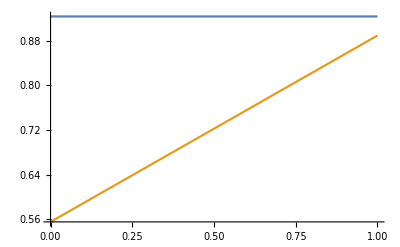

```mathematica
Plot[{0.92358,0.5534326065471977814`6.13498124952187+0.203220260225154347`6.13498124952187 CMax+(0.0016853808792038986`5.624691631549553+0.1310121298570349318`5.624691631549553 CMax)},{CMax,0,1}]
```

```mathematica
ProtocolFidelity1[σ_,CMax_] =FullSimplify[Sqrt[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]^2+EnergyValues[[k]]^2-2*EnergyValues[[l]]*EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].Message4Ket)*(Message4Ket.OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[Message4Ket].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.Message4Ket)) + (1-CMax)*(ConjugateTranspose[Message4Ket].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.Message4Ket))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[Message4Ket].aTypicalProjector.Message4Ket)^2+(1-CMax)*(ConjugateTranspose[Message4Ket].TypicalProjector.Message4Ket)^2)*(GuessKet.Message4Ket)^2],σ∈Reals]
```

√(0.553433+0.20322 CMax+(0.0016854+0.13101 CMax) ⅇ^(-σ^2))

```mathematica
(*Mind your square roots*)
```

```mathematica
ProtocolFidelity[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].Message4Ket)*(Message4Ket.OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[Message4Ket].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.Message4Ket)) + (1-CMax)*(ConjugateTranspose[Message4Ket].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.Message4Ket))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[Message4Ket].aTypicalProjector.Message4Ket)^2+(1-CMax)*(ConjugateTranspose[Message4Ket].TypicalProjector.Message4Ket)^2)*(GuessKet.Message4Ket)^2,σ∈Reals]
```

0.553433+0.20322 CMax+(0.0016854+0.13101 CMax) ⅇ^(-σ^2)

```mathematica
PF[σ_,CMax_]=√(0.5534326065471977814`6.13498124952187+0.203220260225154347`6.13498124952187 CMax+(0.0016853808792038986`5.624691631549553+0.1310121298570349318`5.624691631549553 CMax) ⅇ^(-σ^2))
```

√(0.553433+0.20322 CMax+(0.0016854+0.13101 CMax) ⅇ^(-σ^2))

```mathematica
PF[5,0]
```

0.743931

```mathematica
Sqrt[0.5534326065471977814`6.13498124952187+0.0016853808792038986`5.624691631549553]
```

0.745062

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->20};
```

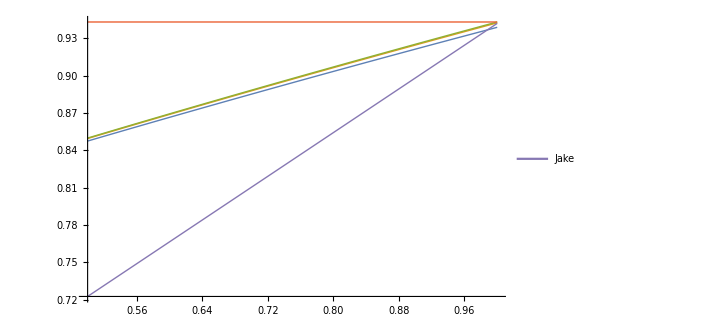

```mathematica
Plot[{PF[0.25,CMax],PF[0.1,CMax],PF[0,CMax],PF[0,1],(1-2*Epsilon)*(CMax)+(1-CMax)*Epsilon^2 + (CMax*Epsilon +(1-CMax*(1-Epsilon)))*0.5},{CMax,0.5,1},BaseStyle->texStyle,PlotStyle->{Thick},AxesLabel->{MaTeX["C_{\\text{Max}}"],MaTeX["\\mathcal{F}"]},PlotLegends->{MaTeX["\\sigma = 0.25"],MaTeX["\\sigma = 0.1"],MaTeX["\\sigma = 0"], MaTeX["\\sigma = 0, C_{\\text{Max}} = 1"],Jake},PlotRange->All]
```

```mathematica
(*Problem! To Evaluate the effectiveness of this bound you have average over all possible messages*)
```

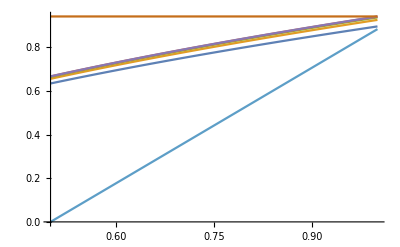

```mathematica
Plot[{PFNG[1,CMax],PFNG[0.5,CMax],PFNG[0.25,CMax],PFNG[0.1,CMax],PFNG[0,CMax],PFNG[0,1],(1-2*Epsilon),(1-2*Epsilon)*(2*CMax-1)},{CMax,0.5,1},BaseStyle->texStyle,PlotStyle->{Thick},AxesLabel->{MaTeX["C_{\\text{Max}}"],MaTeX["\\mathcal{F}"]},PlotLegends->{MaTeX["\\sigma = 0.25"],MaTeX["\\sigma = 0.1"],MaTeX["\\sigma = 0"], MaTeX["\\sigma = 0, C_{\\text{Max}} = 1"]},PlotRange->All]
```

```mathematica
ThreeLetter=KroneckerProduct[Letter,Letter,Letter];
```

```mathematica
Prob = Tr[ThreeLetter.aTypicalProjector]//N
```

0.0580583

```mathematica
Epsilon = 1- Prob
```

```mathematica
Epsilon=0.0580583
```

0.0580583

```mathematica
DephasingFactors[σ_] = Table[ Exp[-(σ*(EnergyValues[[l]]-EnergyValues[[k]]))^2],{l,1,8},{k,1,8}]
```

{{1,1,1,1,ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2)},{1,1,1,1,ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2)},{1,1,1,1,ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2)},{1,1,1,1,ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2)},{ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),1,1,1,1},{ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),1,1,1,1},{ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),1,1,1,1},{ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),ⅇ^(-σ^2),1,1,1,1}}

```mathematica
OverLaps = Total[Table[(EnergyEigenkets[[k]].Message2Ket),{k,1,8}]]
```

1.63699

```mathematica
OverLaps = Table[(Message2Ket.EnergyEigenkets[[k]])*(EnergyEigenkets[[k]].Message2Ket),{k,1,8}]//Total
```

2.66825

```mathematica
Table[ConjugateTranspose[Message4Ket].TypicalProjector.EnergyEigenkets[[l]],{l,1,8}]
```

{0.0564828,-0.178231,0.277516,-0.129458,-0.804435,0.65083,0.807179,0.896026}

```mathematica
ProtocolFidelity[σ_,CMax_] = Flatten[Table[ Exp[-(σ*(EnergyValues[[l]]-EnergyValues[[k]]))^2]*(EnergyEigenkets[[k]].Message4Ket)*(Message4Ket.EnergyEigenkets[[l]])*(CMax*(ConjugateTranspose[Message4Ket].TypicalProjector.EnergyEigenkets[[l]])*(ConjugateTranspose[EnergyEigenkets[[k]]].TypicalProjector.Message4Ket) + (1-CMax)*ConjugateTranspose[Message4Ket].aTypicalProjector.EnergyEigenkets[[l]]*ConjugateTranspose[EnergyEigenkets[[k]]].aTypicalProjector.Message4Ket),{l,1,1},{k,5,5}]]
```

{-0.0793341 (-0.0000393733 (1-CMax)-0.0454368 CMax) ⅇ^(-σ^2)}

```mathematica
EnergyEigenkets[[2]]
```

{-0.18024,0.,0.906127,0.,-0.0746578,0.,0.37533,0.}

```mathematica
CMessages = {Message1Ket,Message2Ket,Message3Ket,Message4Ket,Message5Ket,Message6Ket,Message7Ket,Message8Ket};
```

```mathematica
PF1[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].CMessages[[1]])*(CMessages[[1]].OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[CMessages[[1]]].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.CMessages[[1]])) + (1-CMax)*(ConjugateTranspose[CMessages[[1]]].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.CMessages[[1]]))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[CMessages[[1]]].aTypicalProjector.CMessages[[1]])^2+(1-CMax)*(ConjugateTranspose[CMessages[[1]]].TypicalProjector.CMessages[[1]])^2)*(GuessKet.CMessages[[1]])^2,σ∈Reals]
```

0.553433+0.20322 CMax+(0.0016854+0.13101 CMax) ⅇ^(-σ^2)

```mathematica
PF2[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].CMessages[[2]])*(CMessages[[2]].OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[CMessages[[2]]].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.CMessages[[2]])) + (1-CMax)*(ConjugateTranspose[CMessages[[2]]].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.CMessages[[2]]))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[CMessages[[2]]].aTypicalProjector.CMessages[[2]])^2+(1-CMax)*(ConjugateTranspose[CMessages[[2]]].TypicalProjector.CMessages[[2]])^2)*(GuessKet.CMessages[[2]])^2,σ∈Reals]
```

0.553433+0.20322 CMax+(0.0016854+0.13101 CMax) ⅇ^(-σ^2)

```mathematica
PF3[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].CMessages[[3]])*(CMessages[[3]].OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[CMessages[[3]]].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.CMessages[[3]])) + (1-CMax)*(ConjugateTranspose[CMessages[[3]]].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.CMessages[[3]]))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[CMessages[[3]]].aTypicalProjector.CMessages[[3]])^2+(1-CMax)*(ConjugateTranspose[CMessages[[3]]].TypicalProjector.CMessages[[3]])^2)*(GuessKet.CMessages[[3]])^2,σ∈Reals]
```

0.5534-0.05436 CMax+(0.001685+0.3886 CMax) ⅇ^(-σ^2)

```mathematica
PF4[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].CMessages[[4]])*(CMessages[[4]].OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[CMessages[[4]]].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.CMessages[[4]])) + (1-CMax)*(ConjugateTranspose[CMessages[[4]]].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.CMessages[[4]]))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[CMessages[[4]]].aTypicalProjector.CMessages[[4]])^2+(1-CMax)*(ConjugateTranspose[CMessages[[4]]].TypicalProjector.CMessages[[4]])^2)*(GuessKet.CMessages[[4]])^2,σ∈Reals]
```

0.553433+0.20322 CMax+(0.0016854+0.13101 CMax) ⅇ^(-σ^2)

```mathematica
PF5[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].CMessages[[5]])*(CMessages[[5]].OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[CMessages[[5]]].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.CMessages[[5]])) + (1-CMax)*(ConjugateTranspose[CMessages[[5]]].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.CMessages[[5]]))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[CMessages[[5]]].aTypicalProjector.CMessages[[5]])^2+(1-CMax)*(ConjugateTranspose[CMessages[[5]]].TypicalProjector.CMessages[[5]])^2)*(GuessKet.CMessages[[5]])^2,σ∈Reals]
```

0.5557-0.03227 CMax+(-0.0006028+0.3665 CMax) ⅇ^(-σ^2)

```mathematica
PF6[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].CMessages[[6]])*(CMessages[[6]].OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[CMessages[[6]]].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.CMessages[[6]])) + (1-CMax)*(ConjugateTranspose[CMessages[[6]]].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.CMessages[[6]]))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[CMessages[[6]]].aTypicalProjector.CMessages[[6]])^2+(1-CMax)*(ConjugateTranspose[CMessages[[6]]].TypicalProjector.CMessages[[6]])^2)*(GuessKet.CMessages[[6]])^2,σ∈Reals]
```

0.5557-0.03227 CMax+(-0.0006028+0.3665 CMax) ⅇ^(-σ^2)

```mathematica
PF7[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].CMessages[[7]])*(CMessages[[7]].OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[CMessages[[7]]].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.CMessages[[7]])) + (1-CMax)*(ConjugateTranspose[CMessages[[7]]].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.CMessages[[7]]))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[CMessages[[7]]].aTypicalProjector.CMessages[[7]])^2+(1-CMax)*(ConjugateTranspose[CMessages[[7]]].TypicalProjector.CMessages[[7]])^2)*(GuessKet.CMessages[[7]])^2,σ∈Reals]
```

0.5557-0.1077 CMax+(-0.0006028+0.4419 CMax) ⅇ^(-σ^2)

```mathematica
PF8[σ_,CMax_] =FullSimplify[Total[Flatten[Table[ ((Exp[-σ^2*(EnergyValues[[l]]-EnergyValues[[k]])^2]*(OrthoNormoEnergyEigenkets[[l]].CMessages[[8]])*(CMessages[[8]].OrthoNormoEnergyEigenkets[[k]]))*((CMax*(ConjugateTranspose[CMessages[[8]]].TypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].TypicalProjector.CMessages[[8]])) + (1-CMax)*(ConjugateTranspose[CMessages[[8]]].aTypicalProjector.OrthoNormoEnergyEigenkets[[l]])*(ConjugateTranspose[OrthoNormoEnergyEigenkets[[k]]].aTypicalProjector.CMessages[[8]]))),{l,1,8},{k,1,8}]]]+(CMax*(ConjugateTranspose[CMessages[[8]]].aTypicalProjector.CMessages[[8]])^2+(1-CMax)*(ConjugateTranspose[CMessages[[8]]].TypicalProjector.CMessages[[8]])^2)*(GuessKet.CMessages[[8]])^2,σ∈Reals]
```

0.5611-0.1131 CMax+(-0.005964+0.4473 CMax) ⅇ^(-σ^2)

```mathematica
AvgPF[σ_,CMax_] = FullSimplify[1/8(PF1[σ,CMax]+ PF2[σ,CMax]+ PF3[σ,CMax]+ PF4[σ,CMax]+ PF5[σ,CMax]+ PF6[σ,CMax]+ PF7[σ,CMax]+ PF8[σ,CMax]),σ∈Reals]
```

0.5552+0.03375 CMax+(-0.000129+0.3 CMax) ⅇ^(-σ^2)

```mathematica
GuessOverlaps =Total[ Table[GuessKet.CMessages[[i]],{i,1,8}]]/8
```

```mathematica
1/8 (5/2 Cos[π/8]^3+(7 Cos[π/8]^3)/(2 √2)+3 Cos[π/8]^2 Sin[π/8]+(9 Cos[π/8]^2 Sin[π/8])/(2 √2)+3/2 Cos[π/8] Sin[π/8]^2+(3 Cos[π/8] Sin[π/8]^2)/(2 √2)+Sin[π/8]^3/(2 √2))//N
```

0.788581

```mathematica
Junk[n_,s_] = n - Ceiling[n*s];
```

```mathematica
FidAppend[n_,s_,β_] = (1/2^Junk[n,s])*(1+Tanh[β])^Junk[n,s]
```

2^(-n+Ceiling[n s]) (1+Tanh[β])^(n-Ceiling[n s])

General::munfl: 2.77687/(14124670321394260368352096670161473336688961751845411168136880858571181698427075125580891263167115263733560320843136608276420383806997933833597118572663«1201»798234786740434893458120198341101033812506720046609891160700284002100980452964039788704335302619337597862052192280371481132164147186514169090917191909376) is too small to represent as a normalized machine number; precision may be lost.

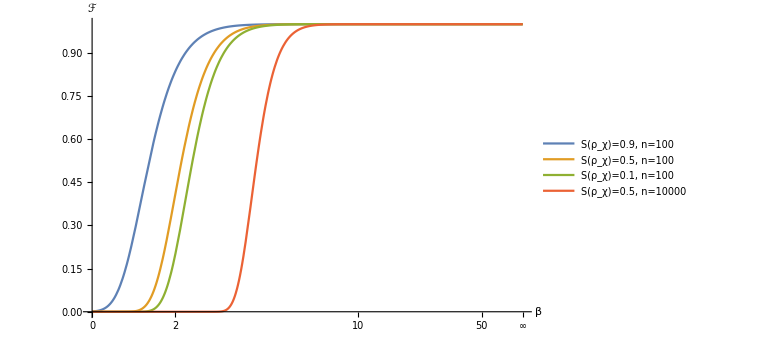

```mathematica
Plot[{FidAppend[100,0.9,β],FidAppend[100,0.5,β],FidAppend[100,0.1,β],FidAppend[10000,0.5,β]},{β,0,∞},PlotLegends->{"S(ρ_χ)=0.9, n=100","S(ρ_χ)=0.5, n=100","S(ρ_χ)=0.1, n=100","S(ρ_χ)=0.5, n=10000"},AxesLabel->{"β","ℱ"}]
```